InterpolatingFunction[…]

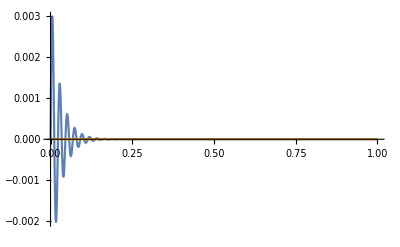

```mathematica
w0 = 278;
Q = 4;
T = 0.001;
th1 = pi / 2;
th1Dot = 0;
v[t_, th_, thDot_]:= 0;
sol=NDSolveValue[{th''[t] + w0/Q th'[t] + w0^2 th[t] == w0^2 v[t], th[0]==0, th'[0]==1}, th, {t, 0, 1}, Method->"ImplicitRungeKutta"]
Plot[{sol[t], v[t]}, {t, 0, 1},PlotRange->Full]
```